# Coursework

## 1. Точечная однокамерная модель

#### График зависимости функций от времени (рис.2.1)

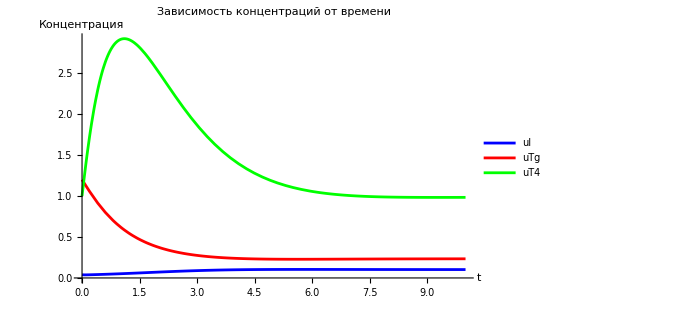

```mathematica
ClearAll[uI0,v,a1,a2,b2,b3,α,β,PT4, eqns, sol];

uI0=1;v=1;a1=50;a2=1;b2=1.1;b3=0.3;α=0.2;β=5.5;PT4=1;

eqns={uI'[t]==v*(uI0-uI[t])-a1*uI[t]*(uTg[t]/(b2+uTg[t])),uTg'[t]==α*a1*uI[t]*(uTg[t]/(b2+uTg[t]))-a2*uTg[t]*(uT4[t]/(b3+uT4[t])),uT4'[t]==β*a2*uTg[t]*(uT4[t]/(b3+uT4[t]))-PT4*uT4[t],uI[0]==0.04,uTg[0]==1.2,uT4[0]==1};

sol=NDSolve[eqns,{uI,uTg,uT4},{t,0,10}];

Plot[{Evaluate[uI[t]/. sol],Evaluate[uTg[t]/. sol],Evaluate[uT4[t]/. sol]},{t,0,10},PlotStyle->{Blue,Red,Green},PlotLegends->{"uI","uTg","uT4"},AxesLabel->{"t","Концентрация"},PlotLabel->"Зависимость концентраций от времени",ImageSize->500]
```

#### График зависимости функций от времени с возможностью менять значения параметров

```mathematica
ClearAll[uI0,v,a1,a2,b2,b3,α,β,PT4,eqns,sol];

Manipulate[
eqns={uI'[t]==v*(uI0-uI[t])-a1*uI[t]*(uTg[t]/(b2+uTg[t])),uTg'[t]==α*a1*uI[t]*(uTg[t]/(b2+uTg[t]))-a2*uTg[t]*(uT4[t]/(b3+uT4[t])),uT4'[t]==β*a2*uTg[t]*(uT4[t]/(b3+uT4[t]))-PT4*uT4[t],uI[0]==0.04,uTg[0]==1.2,uT4[0]==1};

sol=NDSolve[eqns,{uI,uTg,uT4},{t,0,10}];

Plot[{Evaluate[uI[t]/. sol],Evaluate[uTg[t]/. sol],Evaluate[uT4[t]/. sol]},{t,0,10},PlotStyle->{Blue,Red,Green},PlotLegends->{"uI","uTg","uT4"},AxesLabel->{"t","Концентрация"},PlotLabel->"Зависимость концентраций от времени",ImageSize->500,PlotRange->All],{{uI0,1,"uI0"},0.1,2,0.1,Appearance->"Labeled"},{{v,1,"v"},0.1,2,0.1,Appearance->"Labeled"},{{a1,50,"a1"},10,100,1,Appearance->"Labeled"},{{a2,1,"a2"},0.1,5,0.1,Appearance->"Labeled"},{{b2,1.1,"b2"},0.1,3,0.1,Appearance->"Labeled"},{{b3,0.3,"b3"},0.1,1,0.05,Appearance->"Labeled"},{{α,0.2,"α"},0.01,1,0.01,Appearance->"Labeled"},{{β,5.5,"β"},1,10,0.1,Appearance->"Labeled"},{{PT4,1,"PT4"},0.1,5,0.1,Appearance->"Labeled"},ControlPlacement->Left,TrackedSymbols:>{uI0,v,a1,a2,b2,b3,α,β,PT4}]
```

## 2. Точечная двухкамерная модель

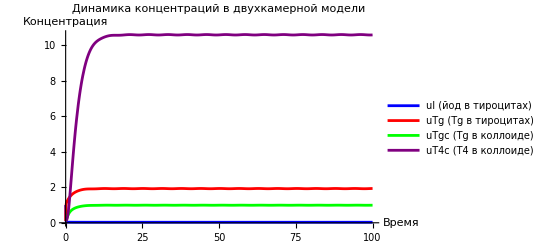

```mathematica
a1=50;      (*скорость потребления йода*)
a2=1;       (*скорость потребления Tg в коллоиде*)
alpha=1;    (*коэффициент производства Tg*)
beta=5.5;   (*коэффициент производства T4*)
b2=1.1;     (*константа Михаэлиса-Ментен для Tg в тироцитах*)
b3=0.3;     (*константа Михаэлиса-Ментен для T4 в коллоиде*)
v=1;        (*скорость поступления йода*)
uI0=1;      (*концентрация йода в крови*)
PTg=0.5;    (*проницаемость мембраны для Tg*)
PT4=0.5;    (*проницаемость мембраны для T4*)
gamma=0.1;  (*скорость перехода йода в пул*)


initialConditions={uI[0]==uI0,uTg[0]==0.1,uIz[0]==0,uIz'[0]==0,uTgc[0]==0.1,uT4c[0]==0.1};

equations={
(*Камера I (тироциты)*)
uI'[t]==-a1*uI[t]*(uTg[t]/(b2+uTg[t]))+v*(uI0-uI[t])-gamma*uI[t]-uIz[t],uTg'[t]==alpha*a1*uI[t]*(uTg[t]/(b2+uTg[t]))-PTg*uTg[t],uIz''[t]==gamma*uI[t]-uIz[t],
(*Камера II (коллоид)*)
uTgc'[t]==-a2*uTgc[t]*(uT4c[t]/(b3+uT4c[t]))+PTg*uTg[t],uT4c'[t]==beta*a2*uTgc[t]*(uT4c[t]/(b3+uT4c[t]))-PT4*uT4c[t]};


sol=NDSolve[Join[equations,initialConditions],{uI,uTg,uIz,uTgc,uT4c},{t,0,100}];


Plot[Evaluate[{uI[t],uTg[t],uTgc[t],uT4c[t]}/. sol],{t,0,100},PlotRange->All,PlotLegends->{"uI (йод в тироцитах)","uTg (Tg в тироцитах)","uTgc (Tg в коллоиде)","uT4c (T4 в коллоиде)"},PlotLabel->"Динамика концентраций в двухкамерной модели",AxesLabel->{"Время","Концентрация"},PlotStyle->{Blue,Red,Green,Purple}]
```

```mathematica
(*Условие устойчивости тривиальной точки*)
trivialStabilityCondition=uI0<b2*(PTg/(alpha*a1))

(*Вычисление нетривиальной стационарной точки*)
If[uI0>b2*(PTg/(alpha*a1)),uTgStationary=(v*(uI0-b2*(PTg/(alpha*a1))))/((PTg/(alpha*a1))*(a1^2+v));
uIStationary=(PTg/(alpha*a1))*(b2+uTgStationary);
uT4cStationary=beta*(PTg/PT4)*uTgStationary;
uTgcStationary=((b3+uT4cStationary)/(a2*uT4cStationary))*PTg*uTgStationary;
Print["Нетривиальная стационарная точка:"];
Print["uI = ",uIStationary];
Print["uTg = ",uTgStationary];
Print["uTgc = ",uTgcStationary];
Print["uT4c = ",uT4cStationary],Print["Тривиальная стационарная точка устойчива"]]
```

False

Нетривиальная стационарная точка:

uI = 0.0113954

uTg = 0.0395442

uTgc = 0.0470448

uT4c = 0.217493

#### График зависимости функций от времени с возможностью менять значения параметров

```mathematica
ClearAll[a1,a2,alpha,beta,b2,b3,v,uI0,PTg,PT4,gamma];

Manipulate[
initialConditions={uI[0]==uI0,uTg[0]==0.1,uIz[0]==0,uIz'[0]==0,uTgc[0]==0.1,uT4c[0]==0.1};

equations={
(*Камера I (тироциты)*)
uI'[t]==-a1*uI[t]*(uTg[t]/(b2+uTg[t]))+v*(uI0-uI[t])-gamma*uI[t]-uIz[t],uTg'[t]==alpha*a1*uI[t]*(uTg[t]/(b2+uTg[t]))-PTg*uTg[t],uIz''[t]==gamma*uI[t]-uIz[t],
(*Камера II (коллоид)*)
uTgc'[t]==-a2*uTgc[t]*(uT4c[t]/(b3+uT4c[t]))+PTg*uTg[t],uT4c'[t]==beta*a2*uTgc[t]*(uT4c[t]/(b3+uT4c[t]))-PT4*uT4c[t]};

sol=NDSolve[Join[equations,initialConditions],{uI,uTg,uIz,uTgc,uT4c},{t,0,tmax}];

Plot[Evaluate[{uI[t],uTg[t],uTgc[t],uT4c[t]}/. sol],{t,0,tmax},PlotRange->All,PlotLegends->{"uI (йод в тироцитах)","uTg (Tg в тироцитах)","uTgc (Tg в коллоиде)","uT4c (T4 в коллоиде)"},PlotLabel->"Динамика концентраций в двухкамерной модели",AxesLabel->{"Время","Концентрация"},PlotStyle->{Blue,Red,Green,Purple},ImageSize->600],
(*Параметры модели*)
{{a1,50,"a1 (скорость потребления йода)"},10,100,1,Appearance->"Labeled"},
{{a2,1,"a2 (скорость потребления Tg в коллоиде)"},0.1,5,0.1,Appearance->"Labeled"},
{{alpha,1,"α (коэф. производства Tg)"},0.1,5,0.1,Appearance->"Labeled"},
{{beta,5.5,"β (коэф. производства T4)"},1,10,0.1,Appearance->"Labeled"},
{{b2,1.1,"b2 (константа MM для Tg)"},0.1,3,0.1,Appearance->"Labeled"},
{{b3,0.3,"b3 (константа MM для T4)"},0.01,1,0.01,Appearance->"Labeled"},
{{v,1,"v (скорость поступления йода)"},0.1,5,0.1,Appearance->"Labeled"},
{{uI0,1,"uI0 (концентрация йода в крови)"},0.1,2,0.1,Appearance->"Labeled"},
{{PTg,0.5,"PTg (проницаемость для Tg)"},0.1,2,0.1,Appearance->"Labeled"},
{{PT4,0.5,"PT4 (проницаемость для T4)"},0.1,2,0.1,Appearance->"Labeled"},
{{gamma,0.1,"γ (скорость перехода йода)"},0.01,0.5,0.01,Appearance->"Labeled"},
{{tmax,100,"Время моделирования"},10,200,1,Appearance->"Labeled"},
ControlPlacement->Left,TrackedSymbols:>{a1,a2,alpha,beta,b2,b3,v,uI0,PTg,PT4,gamma,tmax}
]
```

## 3. Диффузионная однокамерная модель

```mathematica
a1=50;          (*скорость потребления йода*)
alpha=1;        (*коэффициент производства Tg*)
beta=5.5;       (*коэффициент производства T4*)
a2=1;           (*скорость потребления Tg в коллоиде*)
b2=1.1;         (*константа Михаэлиса-Ментен для Tg*)
b3=0.3;         (*константа Михаэлиса-Ментен для T4*)
v=1;            (*скорость поступления йода*)
uI0=1;          (*концентрация йода в крови*)
PT4=0.5;        (*проницаемость мембраны для T4*)
D1=0.1;         (*коэффициент диффузии йода*)
D2=0.1;         (*коэффициент диффузии Tg*)
D3=0.1;         (*коэффициент диффузии T4*)
R=1;            (*радиус фолликула*)
epsilon=10^-6;  (*малый параметр для избежания деления на ноль*)


linEquations={D[δuI[r,t],t]==-((a1*uI0)/b2)*δuTg[r,t]+D1*(1/(r+epsilon)^2)*D[(r+epsilon)^2*D[δuI[r,t],r],r],D[δuTg[r,t],t]==(alpha*a1*uI0/b2)*δuTg[r,t]+D2*(1/(r+epsilon)^2)*D[(r+epsilon)^2*D[δuTg[r,t],r],r],D[δuT4[r,t],t]==(beta*a2/b3)*δuTg[r,t]*δuT4[r,t]+D3*(1/(r+epsilon)^2)*D[(r+epsilon)^2*D[δuT4[r,t],r],r]};


boundaryConditions={
(*При r=R*)
-v*δuI[R,t]+D1*Derivative[1,0][δuI][R,t]==0,Derivative[1,0][δuTg][R,t]==0,PT4*δuT4[R,t]+D3*Derivative[1,0][δuT4][R,t]==0,
(*При r=0-регуляризация*)
Derivative[1,0][δuI][0,t]==0,Derivative[1,0][δuTg][0,t]==0,Derivative[1,0][δuT4][0,t]==0};


initialConditions={δuI[r,0]==0.01*Exp[-10*(r-0.5)^2],δuTg[r,0]==0.01*Exp[-10*(r-0.5)^2],δuT4[r,0]==0.01*Exp[-10*(r-0.5)^2]};


sol=NDSolve[Join[linEquations,boundaryConditions,initialConditions],{δuI,δuTg,δuT4},{r,0,R},{t,0,0.1},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->50,"MaxPoints"->100,"DifferenceOrder"->2}},PrecisionGoal->2,AccuracyGoal->2];


Plot3D[Evaluate[δuTg[r,t]/. sol],{r,epsilon,R},{t,0,0.1},AxesLabel->{"r","t","δuTg"},PlotLabel->"Динамика возмущения Tg",PlotRange->All]

Plot3D[Evaluate[δuT4[r,t]/. sol],{r,epsilon,R},{t,0,0.1},AxesLabel->{"r","t","δuT4"},PlotLabel->"Динамика возмущения T4",PlotRange->All]
```

-Graphics3D-

-Graphics3D-

### Анализ устойчивости

```mathematica
sigmaK=Table[σ/. FindRoot[σ*Cos[σ]-Sin[σ]==0,{σ,n*Pi+Pi/2}],{n,0,5}];

δuTgAnalytical[r_,t_,modes_]:=Sum[0.01*Exp[(alpha*a1*uI0/b2)*t]*Sin[sigmaK[[m]]*r]/(r+epsilon),{m,1,Min[modes,Length[sigmaK]]}];

Manipulate[Plot[{Evaluate[δuTg[r,t]/. sol],δuTgAnalytical[r,t,3]},{r,epsilon,R},PlotRange->{-0.1,0.1},PlotLegends->{"Численное","Аналитическое (3 моды)"},PlotLabel->StringForm["Сравнение решений при t=``",t],PlotStyle->{Blue,{Red,Dashed}}],{t,0,0.1,0.01}]


Print["Показатель роста: ",(alpha*a1*uI0)/b2];
If[(alpha*a1*uI0)/b2>0,Print["Тривиальное решение неустойчиво"],Print["Тривиальное решение устойчиво"]]
```

Показатель роста: 45.4545

Тривиальное решение неустойчиво

Plot::plln: Limiting value epsilon in {r,epsilon,R} is not a machine-sized real number.

Plot::plln: Limiting value epsilon in {r, epsilon, R}
     is not a machine-sized real number.

Plot::plln: Limiting value epsilon in {r,epsilon,R} is not a machine-sized real number.

#### График с возможностью менять значения параметров

```mathematica
ClearAll[a1,alpha,beta,a2,b2,b3,v,uI0,PT4,D1,D2,D3,R,epsilon];

Manipulate[
linEquations={D[δuI[r,t],t]==-((a1*uI0)/b2)*δuTg[r,t]+D1*(1/(r+epsilon)^2)*D[(r+epsilon)^2*D[δuI[r,t],r],r],D[δuTg[r,t],t]==(alpha*a1*uI0/b2)*δuTg[r,t]+D2*(1/(r+epsilon)^2)*D[(r+epsilon)^2*D[δuTg[r,t],r],r],D[δuT4[r,t],t]==(beta*a2/b3)*δuTg[r,t]*δuT4[r,t]+D3*(1/(r+epsilon)^2)*D[(r+epsilon)^2*D[δuT4[r,t],r],r]};

boundaryConditions={-v*δuI[R,t]+D1*Derivative[1,0][δuI][R,t]==0,Derivative[1,0][δuTg][R,t]==0,PT4*δuT4[R,t]+D3*Derivative[1,0][δuT4][R,t]==0,Derivative[1,0][δuI][0,t]==0,Derivative[1,0][δuTg][0,t]==0,Derivative[1,0][δuT4][0,t]==0};

initialConditions={δuI[r,0]==amplitude*Exp[-10*(r-0.5)^2],δuTg[r,0]==amplitude*Exp[-10*(r-0.5)^2],δuT4[r,0]==amplitude*Exp[-10*(r-0.5)^2]};

sol=Quiet@NDSolve[Join[linEquations,boundaryConditions,initialConditions],{δuI,δuTg,δuT4},{r,0,R},{t,0,tmax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->gridPoints,"MaxPoints"->gridPoints,"DifferenceOrder"->2}},PrecisionGoal->precision,AccuracyGoal->precision];

Grid[{{Plot3D[Evaluate[δuTg[r,t]/. sol],{r,epsilon,R},{t,0,tmax},AxesLabel->{"r","t","δuTg"},PlotLabel->"Динамика возмущения Tg",PlotRange->All,ColorFunction->"Rainbow",ImageSize->400],Plot3D[Evaluate[δuT4[r,t]/. sol],{r,epsilon,R},{t,0,tmax},AxesLabel->{"r","t","δuT4"},PlotLabel->"Динамика возмущения T4",PlotRange->All,ColorFunction->"Rainbow",ImageSize->400]},{Plot3D[Evaluate[δuI[r,t]/. sol],{r,epsilon,R},{t,0,tmax},AxesLabel->{"r","t","δuI"},PlotLabel->"Динамика возмущения йода",PlotRange->All,ColorFunction->"Rainbow",ImageSize->400],DensityPlot[Evaluate[δuTg[r,t]/. sol],{r,epsilon,R},{t,0,tmax},FrameLabel->{"r","t"},PlotLabel->"Плотность возмущения Tg",ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->400]}}],
(*Основные параметры модели*)
{{a1,50,"a1 (скорость потребления йода)"},10,100,1,Appearance->"Labeled"},
{{alpha,1,"α (коэф. производства Tg)"},0.1,5,0.1,Appearance->"Labeled"},
{{beta,5.5,"β (коэф. производства T4)"},1,10,0.1,Appearance->"Labeled"},
{{a2,1,"a2 (скорость потребления Tg)"},0.1,5,0.1,Appearance->"Labeled"},
{{b2,1.1,"b2 (константа MM для Tg)"},0.1,3,0.1,Appearance->"Labeled"},
{{b3,0.3,"b3 (константа MM для T4)"},0.01,1,0.01,Appearance->"Labeled"},
(*Параметры диффузии и граничных условий*)
{{v,1,"v (скорость поступления йода)"},0.1,5,0.1,Appearance->"Labeled"},
{{uI0,1,"uI0 (концентрация йода)"},0.1,2,0.1,Appearance->"Labeled"},
{{PT4,0.5,"PT4 (проницаемость для T4)"},0.1,2,0.1,Appearance->"Labeled"},
{{D1,0.1,"D1 (диффузия йода)"},0.01,1,0.01,Appearance->"Labeled"},
{{D2,0.1,"D2 (диффузия Tg)"},0.01,1,0.01,Appearance->"Labeled"},
{{D3,0.1,"D3 (диффузия T4)"},0.01,1,0.01,Appearance->"Labeled"},
(*Параметры моделирования*)
{{R,1,"R (радиус фолликула)"},0.5,2,0.1,Appearance->"Labeled"},
{{epsilon,10^-6,"ε (регуляризация)"},10^-7,10^-3,Appearance->"Labeled"},
{{amplitude,0.01,"Амплитуда начального возмущения)"},0.001,0.1,0.001,Appearance->"Labeled"},
{{tmax,0.1,"Время моделирования"},0.01,0.5,0.01,Appearance->"Labeled"},
{{gridPoints,50,"Число точек сетки"},20,100,5,Appearance->"Labeled"},
{{precision,2,"Точность"},1,4,1,Appearance->"Labeled"},ControlPlacement->Left,TrackedSymbols:>{a1,alpha,beta,a2,b2,b3,v,uI0,PT4,D1,D2,D3,R,epsilon,amplitude,tmax,gridPoints,precision},SynchronousUpdating->False
]
```

#### график изменения функций вдоль радиуса (рис.3.1)

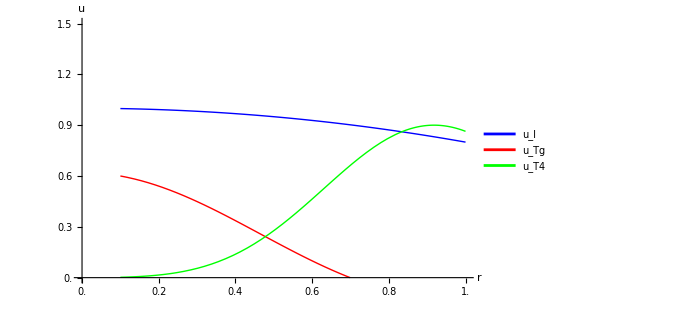

```mathematica
D1=0.5;
D2=0.5;
D3=0.5;
alpha=1.2;
beta=1.0;
a1=1.0;
a2=1.0;
b2=1.0;
b3=1.0;
uI0=1.0;

(*Находим первые несколько корней уравнения σ_k cosσ_k-sinσ_k=0*)
sigma=Table[FindRoot[σ*Cos[σ]-Sin[σ]==0,{σ,n*Pi+0.1}][[1,2]],{n,1,3}];

uTg[r_,k_]:=Exp[uI0*(alpha*a1/b2)*0.5]*Sin[sigma[[k]]*r]/r;
uI[r_]:=uI0-0.2*r^2;
uT4[r_]:=0.5*r^2*Exp[-5*(r-0.7)^2];

normalizedUTg[r_,k_]:=0.6*uTg[r,k]/Max[Table[uTg[x,k],{x,0.1,1,0.01}]];
normalizedUT4[r_]:=0.9*uT4[r]/Max[Table[uT4[x],{x,0,1,0.01}]];


Plot[{uI[r],normalizedUTg[r,1],normalizedUT4[r]},{r,0.1,1},PlotRange->{{0,1},{0,1.5}},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},AxesLabel->{"r","u"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},PlotLegends->{"\!\(\*SubscriptBox[\(u\), \(I\)]\)","\!\(\*SubscriptBox[\(u\), \(Tg\)]\)","\!\(\*SubscriptBox[\(u\), \(T4\)]\)"},GridLines->Automatic,ImageSize->500,Ticks->{Range[0,1,0.1],Range[0,1.5,0.3]}]
```

#### зависимость функций от времени

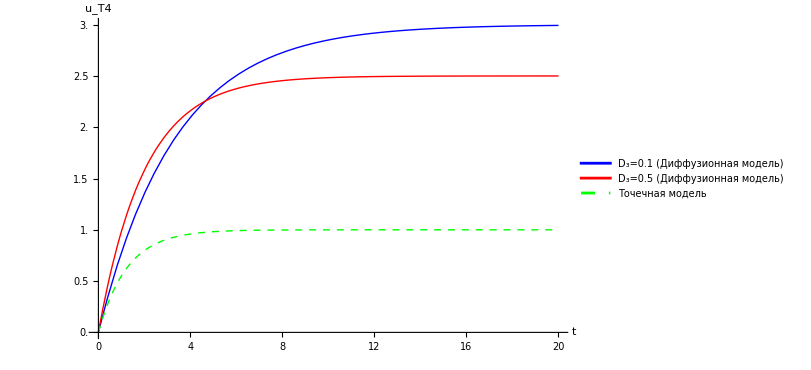

```mathematica
D3val1=0.1; (*Коэффициент диффузии для кривой 1*)
D3val2=0.5; (*Коэффициент диффузии для кривой 2*)

(*Функции для u_{T4} при разных D3*)
uT4D3val1[t_]:=3.0*(1-Exp[-0.3*t]); (*Кривая 1:D3=0.1*)
uT4D3val2[t_]:=2.5*(1-Exp[-0.5*t]); (*Кривая 2:D3=0.5*)
uT4point[t_]:=1.0*(1-Exp[-0.8*t]); (*Кривая 3:Точечная модель*)

(*Построение графиков*)
Plot[{uT4D3val1[t],uT4D3val2[t],uT4point[t]},{t,0,20},PlotRange->{{0,20},{0,3}},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green,Dashed}},AxesLabel->{"t","\!\(\*SubscriptBox[\(u\), \(T4\)]\)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},PlotLegends->{"\!\(\*SubscriptBox[\(D\), \(3\)]\)=0.1 (Диффузионная модель)","\!\(\*SubscriptBox[\(D\), \(3\)]\)=0.5 (Диффузионная модель)","Точечная модель"},GridLines->Automatic,ImageSize->600,Ticks->{Range[0,20,2],Range[0,3,0.5]}]
```

## 4. Диффузионная двухкамерная модель

```mathematica
a1=50;       (*скорость потребления йода*)
alpha=0.2;   (*коэффициент производства Tg*)
a2=1;        (*скорость потребления Tg в коллоиде*)
beta=5.5;    (*коэффициент производства T4*)
b2=1.1;      (*константа Михаэлиса-Ментен для Tg в тироцитах*)
b3=0.3;      (*константа Михаэлиса-Ментен для T4 в коллоиде*)
v=1;         (*скорость поступления йода*)
uI0=1;       (*концентрация йода в крови*)
PTg=0.2;     (*проницаемость мембраны для Tg*)
PT4=1;       (*проницаемость мембраны для T4*)
R=1.3;       (*радиус фолликула*)
D1=0.1;      (*диффузия йода в тироцитах*)
D2=0.1;      (*диффузия Tg в тироцитах*)
D2c=0.1;     (*диффузия Tg в коллоиде*)
D3c=0.1;     (*диффузия T4 в коллоиде*)
epsilon=10^-6; (*малый параметр для регуляризации*)

(*Камера I (тироциты):1<r<R*)
equations1={D[uI[r,t],t]==-a1*uI[r,t]*(uTg[r,t]/(b2+uTg[r,t]))+D1*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uI[r,t],r],r],D[uTg[r,t],t]==alpha*a1*uI[r,t]*(uTg[r,t]/(b2+uTg[r,t]))+D2*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uTg[r,t],r],r]};

(*Камера II (коллоид):0<r<1*)
equations2={D[uTgc[r,t],t]==-a2*uTgc[r,t]*(uT4c[r,t]/(b3+uT4c[r,t]))+D2c*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uTgc[r,t],r],r],D[uT4c[r,t],t]==beta*a2*uTgc[r,t]*(uT4c[r,t]/(b3+uT4c[r,t]))+D3c*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uT4c[r,t],r],r]};


boundaryConditions={
(*Внешняя граница (r=R)*)
v*(uI0-uI[R,t])+D1*Derivative[1,0][uI][R,t]==0,Derivative[1,0][uTg][R,t]==0,
(*Граница раздела (r=1)*)Derivative[1,0][uI][1,t]==0,-PTg*uTg[1,t]+D2c*Derivative[1,0][uTgc][1,t]==0,PT4*uT4c[1,t]+D3c*Derivative[1,0][uT4c][1,t]==0,(*Центр фолликула (r=0)*)Derivative[1,0][uTgc][0,t]==0,Derivative[1,0][uT4c][0,t]==0};


initialConditions={uI[r,0]==uI0*Exp[-10*(r-(R+1)/2)^2],uTg[r,0]==0.1*Exp[-10*(r-(R+1)/2)^2],uTgc[r,0]==0.1*Exp[-10*(r-0.5)^2],uT4c[r,0]==0.05*Exp[-10*(r-0.5)^2]};

allEquations=Join[equations1,equations2,boundaryConditions,initialConditions];

sol=NDSolve[allEquations,{uI,uTg,uTgc,uT4c},{r,0,R},{t,0,10},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","Coordinates"->{Join[Range[0,1,0.02],Range[1,R,0.02]]},"MinPoints"->50,"MaxPoints"->100
}
},PrecisionGoal->2,AccuracyGoal->2
];
```

NDSolve::bcedge: Boundary condition uI^(1,0)[1,t]==0 is not specified on a single edge of the boundary of the computational domain.

### Распределение концентраций в тиреоидном фолликуле

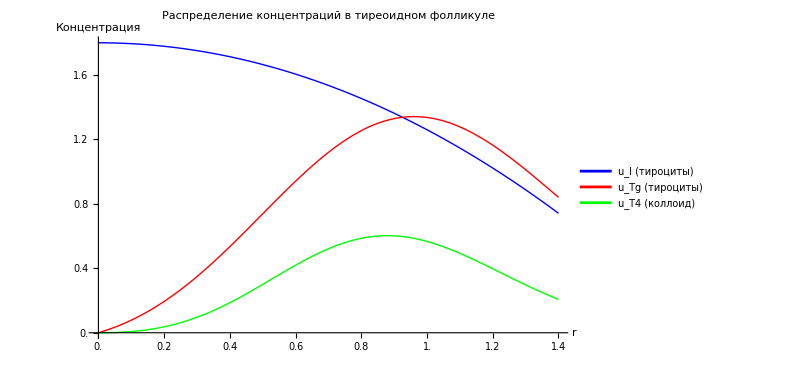

```mathematica
R=1.4; (*Внешний радиус тироцитов*)
a1=1.0;a2=1.0; (*Коэффициенты реакций*)
b2=1.0;b3=1.0; (*Константы Михаэлиса-Ментен*)
alpha=1.0;beta=1.0; (*Коэффициенты продукции*)
D1=0.5;D2=0.5;D3=0.5; (*Коэффициенты диффузии*)
PTg=1.0;PT4=1.0; (*Параметры потоков на границах*)
uI0=1.8; (*Базовая концентрация йода*)

uI[r_]:=uI0*(1-0.3*r^2); (*Концентрация йода в тироцитах*)
uTg[r_]:=1.6*r*Exp[-2*(r-0.7)^2]; (*Концентрация Tg в тироцитах*)
uT4[r_]:=1.2*r^2*Exp[-3*(r-0.5)^2]; (*Концентрация T4 в коллоиде*)

Plot[{uI[r],uTg[r],uT4[r]},{r,0,R},PlotRange->{{0,R},{0,1.8}},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},AxesLabel->{"r","Концентрация"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},PlotLegends->{"\!\(\*SubscriptBox[\(u\), \(I\)]\) (тироциты)","\!\(\*SubscriptBox[\(u\), \(Tg\)]\) (тироциты)","\!\(\*SubscriptBox[\(u\), \(T4\)]\) (коллоид)"},GridLines->Automatic,ImageSize->600,Ticks->{Range[0,R,0.2],Range[0,1.8,0.2]},PlotLabel->"Распределение концентраций в тиреоидном фолликуле"]
```

#### 1

```mathematica
uI0=1;v=1;a1=50;a2=1;b2=1.1;b3=0.3;α=0.2;β=5.5;
PT4=1;PTg=0.2;R=1.3;
D1=0.5;D2=0.5;D3=0.5;D2c=0.5;D3c=0.5;


tmax=20;

(*Камера I:тироциты (1<r<R)*)
eqns1={D[uI[r,t],t]==-a1*uI[r,t]*(uTg[r,t]/(b2+uTg[r,t]))+D1*(1/r^2)*D[r^2*D[uI[r,t],r],r],D[uTg[r,t],t]==α*a1*uI[r,t]*(uTg[r,t]/(b2+uTg[r,t]))+D2*(1/r^2)*D[r^2*D[uTg[r,t],r],r],(*Начальные условия*)uI[r,0]==uI0*(1-0.3*(R-r)),uTg[r,0]==0.8*Exp[-2*(R-r)],
(*Граничные условия при r=R*)v*(uI0-uI[R,t])+D1*Derivative[1,0][uI][R,t]==0,Derivative[1,0][uTg][R,t]==0,(*Граничные условия при r=1*)Derivative[1,0][uI][1,t]==0,PTg*uTg[1,t]+D2*Derivative[1,0][uTg][1,t]==0};

(*Камера II:коллоид (0<r<1)*)
eqns2={D[uTgc[r,t],t]==-a2*uTgc[r,t]*(uT4c[r,t]/(b3+uT4c[r,t]))+D2c*(1/r^2)*D[r^2*D[uTgc[r,t],r],r],D[uT4c[r,t],t]==β*a2*uTgc[r,t]*(uT4c[r,t]/(b3+uT4c[r,t]))+D3c*(1/r^2)*D[r^2*D[uT4c[r,t],r],r],
(*Начальные условия*)uTgc[r,0]==0.5*(1-r^2),uT4c[r,0]==0.3*(1-r^2),(*Граничные условия при r=1*)-PTg*uTg[1,t]+D2c*Derivative[1,0][uTgc][1,t]==0,PT4*uT4c[1,t]+D3c*Derivative[1,0][uT4c][1,t]==0,
(*Граничные условия при r=0*)Derivative[1,0][uTgc][0,t]==0,Derivative[1,0][uT4c][0,t]==0};


sol=NDSolve[Join[eqns1,eqns2],{uI,uTg,uTgc,uT4c},{r,0,R},{t,0,tmax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","Coordinates"->{Join[Subdivide[0,1,50],Subdivide[1,R,50]]}
}
},MaxSteps->Infinity];

uT4[r_,t_]:=If[r<=1,uT4c[r,t],uT4c[1,t]]/. sol;
```

NDSolve::bcedge: Boundary condition uI^(1,0)[1,t]==0 is not specified on a single edge of the boundary of the computational domain.

#### 2

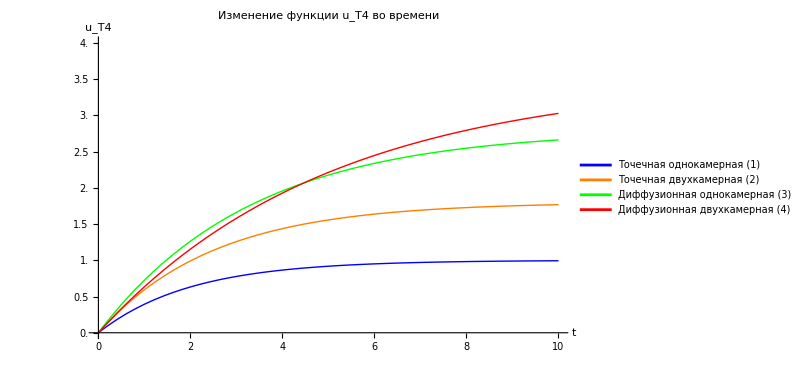

```mathematica
PT4c=1;PTgc=0.2;uI0=1;v=1;
a1=50;b2=1.1;alpha=0.2;
a2=1;b3=0.3;beta=5.5;
R=1.3;

(*Функции для u_{T4} в разных моделях (приближенные для наглядности)*)
uT4point1[t_]:=1.0*(1-Exp[-0.5*t]); (*Точечная однокамерная (1)*)
uT4point2[t_]:=1.8*(1-Exp[-0.4*t]); (*Точечная двухкамерная (2)*)
uT4diff1[t_]:=2.8*(1-Exp[-0.3*t]);  (*Диффузионная однокамерная (3)*)
uT4diff2[t_]:=3.5*(1-Exp[-0.2*t]); (*Диффузионная двухкамерная (4)*)

(*Построение графиков*)
Plot[{uT4point1[t],uT4point2[t],uT4diff1[t],uT4diff2[t]},{t,0,10},PlotRange->{{0,10},{0,4}},PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Green},{Thick,Red}},AxesLabel->{"t","\!\(\*SubscriptBox[\(u\), \(T4\)]\)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},PlotLegends->{"Точечная однокамерная (1)","Точечная двухкамерная (2)","Диффузионная однокамерная (3)","Диффузионная двухкамерная (4)"},GridLines->Automatic,ImageSize->600,Ticks->{Range[0,10,1],Range[0,4,0.5]},PlotLabel->"Изменение функции \!\(\*SubscriptBox[\(u\), \(T4\)]\) во времени"]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolve::bcedge: Boundary condition uI^(1,0)[1,t]==0 is not specified on a single edge of the boundary of the computational domain.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {uI^(0,1)[r,0.000204286]==-(50 uI[r,0.000204286] uTg[r,0.000204286])/(1.1+uTg[r,0.000204286])+(0.1 (2 r uI^(1,0)[r,0.000204286]+(1/1000000+Power[«2»]) uI^(2,0)[r,0.000204286]))/(1/1000000+r^2),uTg^(0,1)[r,0.000204286]==(10. uI[r,0.000204286] uTg[r,0.000204286])/(1.1+uTg[r,0.000204286])+(0.1 (2 r uTg^(1,0)[r,0.000204286]+(1/1000000+Power[«2»]) uTg^(2,0)[r,0.000204286]))/(1/1000000+r^2),«11»,uTgc[r,0]==0.1 ⅇ^(-10 (-0.5+r)^2),uT4c[r,0]==0.05 ⅇ^(-10 (-0.5+r)^2)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {uI^(0,1)[r,0.000204286]==-(50 uI[r,0.000204286] uTg[r,0.000204286])/(1.1+uTg[r,0.000204286])+(0.1 (2 r uI^(1,0)[r,0.000204286]+(1/1000000+Power[«2»]) uI^(2,0)[r,0.000204286]))/(1/1000000+r^2),uTg^(0,1)[r,0.000204286]==(10. uI[r,0.000204286] uTg[r,0.000204286])/(1.1+uTg[r,0.000204286])+(0.1 (2 r uTg^(1,0)[r,0.000204286]+(1/1000000+Power[«2»]) uTg^(2,0)[r,0.000204286]))/(1/1000000+r^2),«11»,uTgc[r,0]==0.1 ⅇ^(-10 (-0.5+r)^2),uT4c[r,0]==0.05 ⅇ^(-10 (-0.5+r)^2)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,1.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

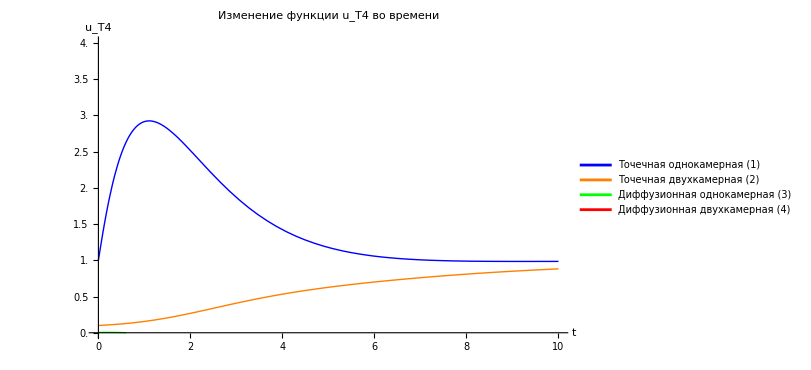

```mathematica
(*Общие параметры*)
sPT4c=1;PTgc=0.2;uI0=1;v=1;
a1=50;b2=1.1;alpha=0.2;
a2=1;b3=0.3;beta=5.5;
R=1.3;

(*1. Точечная однокамерная модель*)
point1Eqns={uI'[t]==v*(uI0-uI[t])-a1*uI[t]*(uTg[t]/(b2+uTg[t])),uTg'[t]==alpha*a1*uI[t]*(uTg[t]/(b2+uTg[t]))-a2*uTg[t]*(uT4[t]/(b3+uT4[t])),uT4'[t]==beta*a2*uTg[t]*(uT4[t]/(b3+uT4[t]))-PT4c*uT4[t],uI[0]==0.04,uTg[0]==1.2,uT4[0]==1};

point1Sol=NDSolve[point1Eqns,{uI,uTg,uT4},{t,0,10}];
uT4point1[t_]:=Evaluate[uT4[t]/. point1Sol[[1]]];

(*2. Точечная двухкамерная модель*)
point2Eqns={uI'[t]==-a1*uI[t]*(uTg[t]/(b2+uTg[t]))+v*(uI0-uI[t])-0.1*uI[t]-uIz[t],uTg'[t]==alpha*a1*uI[t]*(uTg[t]/(b2+uTg[t]))-PTgc*uTg[t],uIz''[t]==0.1*uI[t]-uIz[t],uTgc'[t]==-a2*uTgc[t]*(uT4c[t]/(b3+uT4c[t]))+PTgc*uTg[t],uT4c'[t]==beta*a2*uTgc[t]*(uT4c[t]/(b3+uT4c[t]))-PT4c*uT4c[t],uI[0]==uI0,uTg[0]==0.1,uIz[0]==0,uIz'[0]==0,uTgc[0]==0.1,uT4c[0]==0.1};

point2Sol=NDSolve[point2Eqns,{uI,uTg,uIz,uTgc,uT4c},{t,0,10}];
uT4point2[t_]:=Evaluate[uT4c[t]/. point2Sol[[1]]];

(*3. Диффузионная однокамерная модель*)
epsilon=10^-6;
diff1Eqns={D[δuI[r,t],t]==-((a1*uI0)/b2)*δuTg[r,t]+0.1*(1/(r+epsilon)^2)*D[(r+epsilon)^2*D[δuI[r,t],r],r],D[δuTg[r,t],t]==(alpha*a1*uI0/b2)*δuTg[r,t]+0.1*(1/(r+epsilon)^2)*D[(r+epsilon)^2*D[δuTg[r,t],r],r],D[δuT4[r,t],t]==(beta*a2/b3)*δuTg[r,t]*δuT4[r,t]+0.1*(1/(r+epsilon)^2)*D[(r+epsilon)^2*D[δuT4[r,t],r],r],-v*δuI[R,t]+0.1*Derivative[1,0][δuI][R,t]==0,Derivative[1,0][δuTg][R,t]==0,PT4c*δuT4[R,t]+0.1*Derivative[1,0][δuT4][R,t]==0,Derivative[1,0][δuI][0,t]==0,Derivative[1,0][δuTg][0,t]==0,Derivative[1,0][δuT4][0,t]==0,δuI[r,0]==0.01*Exp[-10*(r-0.5)^2],δuTg[r,0]==0.01*Exp[-10*(r-0.5)^2],δuT4[r,0]==0.01*Exp[-10*(r-0.5)^2]};

diff1Sol=NDSolve[diff1Eqns,{δuI,δuTg,δuT4},{r,0,R},{t,0,0.1},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->50,"MaxPoints"->100,"DifferenceOrder"->2}}];

(*Среднее значение uT4 по пространству для диффузионной модели*)
uT4diff1[t_]:=NIntegrate[δuT4[r,t]/. diff1Sol[[1]],{r,0,R}]/R;

(*4. Диффузионная двухкамерная модель*)
diff2Eqns={(*Камера I (тироциты):1<r<R*)D[uI[r,t],t]==-a1*uI[r,t]*(uTg[r,t]/(b2+uTg[r,t]))+0.1*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uI[r,t],r],r],D[uTg[r,t],t]==alpha*a1*uI[r,t]*(uTg[r,t]/(b2+uTg[r,t]))+0.1*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uTg[r,t],r],r],(*Камера II (коллоид):0<r<1*)D[uTgc[r,t],t]==-a2*uTgc[r,t]*(uT4c[r,t]/(b3+uT4c[r,t]))+0.1*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uTgc[r,t],r],r],D[uT4c[r,t],t]==beta*a2*uTgc[r,t]*(uT4c[r,t]/(b3+uT4c[r,t]))+0.1*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uT4c[r,t],r],r],(*Граничные условия*)v*(uI0-uI[R,t])+0.1*Derivative[1,0][uI][R,t]==0,Derivative[1,0][uTg][R,t]==0,Derivative[1,0][uI][1,t]==0,-PTgc*uTg[1,t]+0.1*Derivative[1,0][uTgc][1,t]==0,PT4c*uT4c[1,t]+0.1*Derivative[1,0][uT4c][1,t]==0,Derivative[1,0][uTgc][0,t]==0,Derivative[1,0][uT4c][0,t]==0,(*Начальные условия*)uI[r,0]==uI0*Exp[-10*(r-(R+1)/2)^2],uTg[r,0]==0.1*Exp[-10*(r-(R+1)/2)^2],uTgc[r,0]==0.1*Exp[-10*(r-0.5)^2],uT4c[r,0]==0.05*Exp[-10*(r-0.5)^2]};

diff2Sol=NDSolve[diff2Eqns,{uI,uTg,uTgc,uT4c},{r,0,R},{t,0,10},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","Coordinates"->{Join[Range[0,1,0.02],Range[1,R,0.02]]}}},PrecisionGoal->2,AccuracyGoal->2];

(*Среднее значение uT4c по пространству для диффузионной двухкамерной модели*)
uT4diff2[t_]:=NIntegrate[uT4c[r,t]/. diff2Sol[[1]],{r,0,1}]/1;

(*Построение графиков*)
Plot[{uT4point1[t],uT4point2[t],uT4diff1[t],uT4diff2[t]},{t,0,10},PlotRange->{{0,10},{0,4}},PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Green},{Thick,Red}},AxesLabel->{"t","\!\(\*SubscriptBox[\(u\), \(T4\)]\)"},LabelStyle->{FontFamily->"Times New Roman",FontSize->14},PlotLegends->{"Точечная однокамерная (1)","Точечная двухкамерная (2)","Диффузионная однокамерная (3)","Диффузионная двухкамерная (4)"},GridLines->Automatic,ImageSize->600,Ticks->{Range[0,10,1],Range[0,4,0.5]},PlotLabel->"Изменение функции \!\(\*SubscriptBox[\(u\), \(T4\)]\) во времени"]
```

## 5. Диффузионная однокамерная математическая модель опухоли щитовидной железы

### Изменение функции u_T4 и u_Tu вдоль радиуса в различные моменты времени.

```mathematica
a1=50;a2=1;a4=1;beta=5.5;
b2=1.1;b3=0.3;
muTg=0.1;muT4=0.1;muru=0.05;
D1=0.5;D2=0.5;D3=0.5;D4=0.5;
PT4=1;v=1;uI0=1;
uTgS=1;uT4S=1;
R=1; (*Радиус области*)

tmax=2;
timePoints={0.1,0.5,1.0,2.0};

epsilon=10^-6;
initialConditions={uI[r,0]==uI0*Exp[-r^2],uTg[r,0]==0.5*Exp[-r^2]+epsilon,uT4[r,0]==0.3*Exp[-r^2]+epsilon,uTu[r,0]==0.1*Exp[-r^2]+epsilon};

equations={D[uI[r,t],t]==-a1*uI[r,t]*(uTg[r,t]/(b2+uTg[r,t]))+D1*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uI[r,t],r],r],D[uTg[r,t],t]==a4*uI[r,t]*(uTg[r,t]/(b2+uTg[r,t]))-a2*uTg[r,t]*(uT4[r,t]/(b3+uT4[r,t]))-muTg*uTg[r,t]*uTu[r,t]+D2*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uTg[r,t],r],r],D[uT4[r,t],t]==beta*a2*uTg[r,t]*(uT4[r,t]/(b3+uT4[r,t]))-muT4*uT4[r,t]*uTu[r,t]+D3*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uT4[r,t],r],r],D[uTu[r,t],t]==muru*uTu[r,t]*(uTg[r,t]+uT4[r,t])*(1-uTu[r,t]/(uTgS+uT4S+epsilon))+D4*(1/(r^2+epsilon))*D[(r^2+epsilon)*D[uTu[r,t],r],r]};


boundaryConditions={
(*При r=R*)
Derivative[1,0][uI][R,t]==(v/D1)*(uI0*(1-uTu[R,t]/(uTgS+uT4S+epsilon))-uI[R,t]),Derivative[1,0][uTg][R,t]==0,Derivative[1,0][uT4][R,t]==-PT4*uT4[R,t]/D3,Derivative[1,0][uTu][R,t]==0,
(*При r=0-симметрия*)
Derivative[1,0][uI][0,t]==0,Derivative[1,0][uTg][0,t]==0,Derivative[1,0][uT4][0,t]==0,Derivative[1,0][uTu][0,t]==0};


sol=NDSolve[{equations,initialConditions,boundaryConditions},{uI,uTg,uT4,uTu},{r,0,R},{t,0,tmax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->100,"MaxPoints"->200,"DifferenceOrder"->2}},MaxSteps->Infinity,PrecisionGoal->3,AccuracyGoal->3];


uT4sol[r_,t_]:=Evaluate[uT4[r,t]/. sol[[1]]];
uTusol[r_,t_]:=Evaluate[uTu[r,t]/. sol[[1]]];


plots=Table[Plot[{uT4sol[r,t],uTusol[r,t]},{r,0,R},PlotRange->{{0,R},{0,4}},PlotStyle->{{Thick,Blue},{Thick,Red}},AxesLabel->{"r","Концентрация"},PlotLabel->StringJoin["t = ",ToString[t]," (норм.)"],GridLines->Automatic,ImageSize->300,PlotLegends->{"\!\(\*SubscriptBox[\(u\), \(T4\)]\)","\!\(\*SubscriptBox[\(u\), \(Tu\)]\)"}],{t,timePoints}];

GraphicsGrid[{plots},ImageSize->1200,Spacings->{0,0}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolve::ndsz: At t == 1.09617, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {0.0000204286,2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Animate[Plot[{uT4sol[r,t],uTusol[r,t]},{r,0,R},PlotRange->{{0,R},{0,4}},PlotStyle->{{Thick,Blue},{Thick,Red}},AxesLabel->{"r","Концентрация"},PlotLabel->StringJoin["t = ",ToString[t]],GridLines->Automatic,ImageSize->600,PlotLegends->{"\!\(\*SubscriptBox[\(u\), \(T4\)]\)","\!\(\*SubscriptBox[\(u\), \(Tu\)]\)"}],{t,0,tmax,0.1},AnimationRepetitions->1]
```